# h=C+D+C^-1+D^-1

norm extrapolation for the paper
“COMPUTATIONAL EXPLORATIONS OF THE THOMPSON GROUP T FOR THE AMENABILITY PROBLEM OF F” 
by S. Haagerup, U. Haagerup, M. Ramirez-Solano:

```mathematica
norms={{1,2.},{2,2.7386127875258306},{3,3.055703412859072},{4,3.2586121569734106},{5,3.4292609360165467},{6,3.5187496979405797},{7,3.5785926127769545},{8,3.6136924357999027},{9,3.639563973564201},{10,3.6640652912973164},{11,3.6811799245405408},{12,3.6970415388301285},{13,3.7088089364021144},{14,3.718835559697048},{15,3.7289515865989724},{16,3.736356750583295},{17,3.743544352777439},{18,3.7493533842351234},{19,3.7548227934145477},{20,3.760297930689068},{21,3.764546154871844},{22,3.768760183628806},{23,3.7722698721396735},{24,3.775826287530374},{25,3.779237970007282},{26,3.7820536826018443},{27,3.784897763209191},{28,3.787301509017402}}
Ntuple=Length[norms]
Mnorm=norms[[#]][[2]]&;
```

{{1,2.},{2,2.73861},{3,3.0557},{4,3.25861},{5,3.42926},{6,3.51875},{7,3.57859},{8,3.61369},{9,3.63956},{10,3.66407},{11,3.68118},{12,3.69704},{13,3.70881},{14,3.71884},{15,3.72895},{16,3.73636},{17,3.74354},{18,3.74935},{19,3.75482},{20,3.7603},{21,3.76455},{22,3.76876},{23,3.77227},{24,3.77583},{25,3.77924},{26,3.78205},{27,3.7849},{28,3.7873}}

28

```mathematica
Table[{i,Mnorm[i]^2},{i,1,Ntuple}]
```

{{1,4.},{2,7.5},{3,9.33732},{4,10.6186},{5,11.7598},{6,12.3816},{7,12.8063},{8,13.0588},{9,13.2464},{10,13.4254},{11,13.5511},{12,13.6681},{13,13.7553},{14,13.8297},{15,13.9051},{16,13.9604},{17,14.0141},{18,14.0577},{19,14.0987},{20,14.1398},{21,14.1718},{22,14.2036},{23,14.23},{24,14.2569},{25,14.2826},{26,14.3039},{27,14.3255},{28,14.3437}}

```mathematica
Table[{i,Mnorm[i]^2},{i,1,Ntuple}]//MatrixForm
```

(1 | 4.
2 | 7.5
3 | 9.33732
4 | 10.6186
5 | 11.7598
6 | 12.3816
7 | 12.8063
8 | 13.0588
9 | 13.2464
10 | 13.4254
11 | 13.5511
12 | 13.6681
13 | 13.7553
14 | 13.8297
15 | 13.9051
16 | 13.9604
17 | 14.0141
18 | 14.0577
19 | 14.0987
20 | 14.1398
21 | 14.1718
22 | 14.2036
23 | 14.23
24 | 14.2569
25 | 14.2826
26 | 14.3039
27 | 14.3255
28 | 14.3437)

```mathematica
myFit=Function[{a,d},Module[{b,c,ori,model,fit,res1,res2,diff,var,},
(*Clear[aa,b,cc,d];*)
(*d=0;*)
ori=Table[{i,Mnorm[i]^2},{i,1,Ntuple}];
(*aa=11.66*)
model=a-b ((x-d )^(-c));
fit=FindFit[ori[[Range[Length[ori]-10,Length[ori]]]],model,{b,c},x];
res1=Table[model/.fit,{x,1,Ntuple,1}];
res2=Table[Mnorm[i]^2,{i,1,Ntuple,1}];
diff=Drop[(res1-res2)^2,1];
var=Total[diff]/(Ntuple-1);
(*Print["V= ",variance," fit(a,b,c,d)= ",{a,b,c,d}/.fit];*)
{var,{a,b,c,d}/.fit}
]]
modelf=Function[args,Module[{a,b,c,d},{a,b,c,d}=args;a-b ((x-d )^(-c))]]
modelff=Function[args,Module[{a,b,c,d},{a,b,c,d}=args;a-b ((#-d )^(-c))&]]
plot=Function[f,ListPlot[Table[{x,f[x]},{x,0.01,Ntuple,.01}],PlotStyle->{Red,PointSize[.002]}]];
```

Function[{a,d},Module[{b,c,ori,model,fit,res1,res2,diff,var,Null},ori=Table[{i,Mnorm[i]^2},{i,1,Ntuple}];model=a-b (x-d)^-c;fit=FindFit[ori⟦Range[Length[ori]-10,Length[ori]]⟧,model,{b,c},x];res1=Table[model/.fit,{x,1,Ntuple,1}];res2=Table[Mnorm[i]^2,{i,1,Ntuple,1}];diff=Drop[(res1-res2)^2,1];var=Total[diff]/(Ntuple-1);{var,{a,b,c,d}/.fit}]]

Function[args,Module[{a,b,c,d},{a,b,c,d}=args;a-b (x-d)^-c]]

Function[args,Module[{a,b,c,d},{a,b,c,d}=args;a-b (#1-d)^-c&]]

```mathematica
fits=Flatten[Table[myFit[aa,d],{aa,14,16,.1},{d,-1,1,.2}],1];
xxxByExtrapolatedNorm=Table[fits⟦i⟧⟦2⟧⟦1⟧,{i,1,Length[fits]}];
fits=fits[[Ordering[xxxByExtrapolatedNorm]]];
ori=Table[{i,Mnorm[i]^2},{i,1,Ntuple}];
pics=Table[Show[ListPlot[ori,PlotLabel->ToString[i]<>":"<>ToString[fits⟦i⟧],PlotRange->{0,16}],plot[modelff[fits⟦i,2⟧]]],{i,1,Length[fits]}];
```

Power::infy: Infinite expression 1/0.^18.6449 encountered.

Power::infy: Infinite expression 1/0.^12.2799 encountered.

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindFit :: cvmit will be suppressed during this calculation.

Power::infy: Infinite expression 1/0.^11.9366 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0.^18.9426 encountered.

Power::infy: Infinite expression 1/0.^18.6449 encountered.

Power::infy: Infinite expression 1/0.^12.4908 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
(*Sorted by extrapolated norm*)
Manipulate[pics[[i]],{i,1,Length[pics],1}]
```

```mathematica
good 
excellent
Chosen
```

14.8-21.0431/(0.8+x)^1.13967

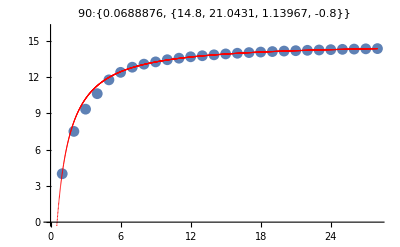

```mathematica
modelf[fits⟦90⟧⟦2⟧]
pics⟦90⟧
```

```mathematica
fitsV=Flatten[Table[myFit[aa,d],{aa,14,16,.1},{d,-1,1,.2}],1];
xxxByVariance=Table[fitsV⟦i⟧⟦1⟧,{i,1,Length[fitsV]}];
fitsV=fitsV[[Ordering[xxxByVariance]]];
oriV=Table[{i,Mnorm[i]^2},{i,1,Ntuple}];
picsV=Table[Show[ListPlot[oriV,AspectRatio->1,PlotLabel->ToString[i]<>":"<>ToString[fitsV⟦i⟧],PlotRange->{0,16},ImageSize->{800,800},PlotStyle->{PointSize[.01]}],plot[modelff[fitsV⟦i,2⟧]]],{i,1,Length[fitsV]}];
```

Power::infy: Infinite expression 1/0.^18.6449 encountered.

Power::infy: Infinite expression 1/0.^12.2799 encountered.

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindFit :: cvmit will be suppressed during this calculation.

Power::infy: Infinite expression 1/0.^11.9366 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

Power::infy: Infinite expression 1/0.^0.790781 encountered.

Power::infy: Infinite expression 1/0.^0.783355 encountered.

Power::infy: Infinite expression 1/0.^0.69507 encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

```mathematica
(*Sorted by variance*)
Manipulate[picsV[[i]],{i,1,Length[pics],1},ContentSize->{900,900}]
```

good 
excellent 
superexcellent
Chosen

14.8-18.5975/(0.2+x)^1.10972

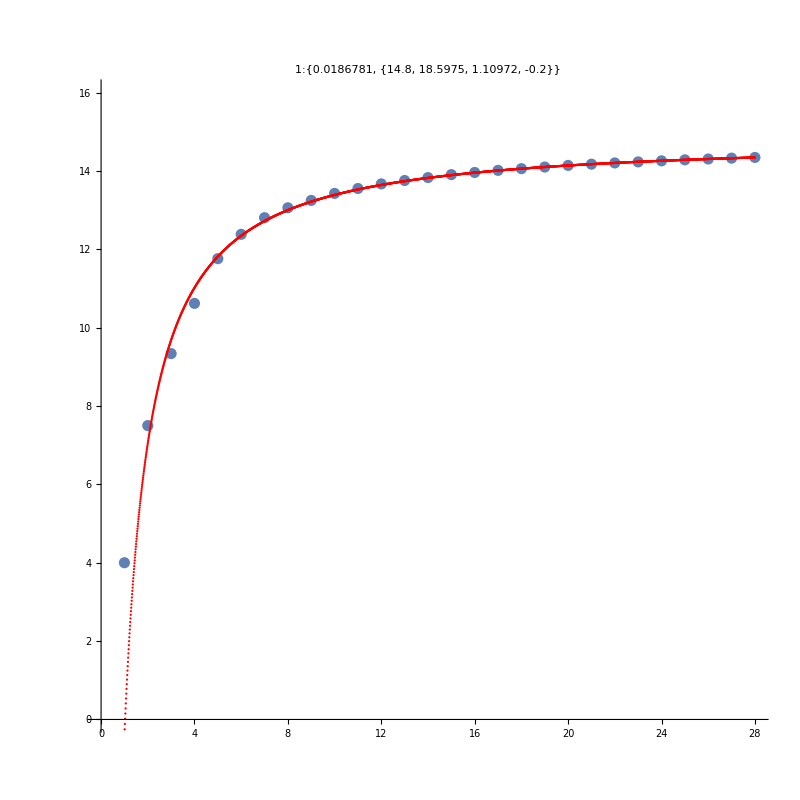

```mathematica
modelf[fitsV⟦1⟧⟦2⟧]
picsV⟦1⟧
```

```mathematica
Sqrt[14.8]
```

3.84708

```mathematica
(*Run .nb program that computes norms. But run first Clear[Mnorm]*)
```

```mathematica
Clear[Mnorm]
```

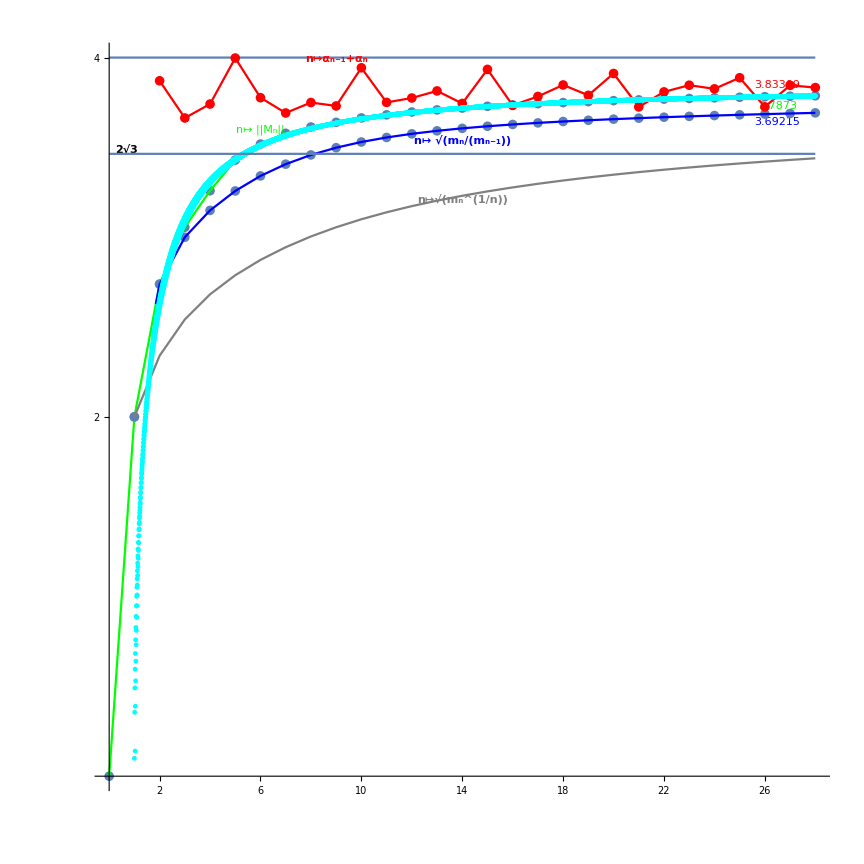

```mathematica
ma[0]=1;
Table[ma[i]=m⟦i⟧,{i,1,Length[m]}];
Show[
ListPlot[Table[{i,Mnorm[i]},{i,0,Ntuple}],Ticks->{Range[2,Ntuple,2]},PlotStyle->{PointSize[.008]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]},PlotRange->{0,4},AspectRatio->1],
ListPlot[Table[{i,Mnorm[i]},{i,0,Ntuple}],Joined->True,PlotStyle->{Green}],
Graphics[{Green,Text[Style[HoldForm["n↦ ||M_n||"],Large],{6,.08+Mnorm[6]}]}],
Graphics[{Green,Text[Style[Mnorm[Ntuple],Large],{Ntuple-1.5,-.055+Mnorm[Ntuple]}]}],
Graphics[{Red,Text[Style[N[α[Ntuple-1]+α[Ntuple]],Large],{Ntuple-1.5,.015+α[Ntuple-1]+α[Ntuple]}]}],
Graphics[{Blue,Text[Style[N[(ma[Ntuple]/ma[Ntuple-1])^(1/2)],Large],{Ntuple-1.5,-.05+(ma[Ntuple]/ma[Ntuple-1])^(1/2)}]}],
Plot[8,{x,0,Ntuple}],
ListPlot[Table[{i,(ma[i]/ma[i-1])^(1/2)},{i,1,Ntuple}],Ticks->{Range[2,Ntuple,2]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]},PlotStyle->{PointSize[.008]}],
ListPlot[Table[{i,(ma[i]/ma[i-1])^(1/2)},{i,1,Ntuple,1}],Joined->True,PlotStyle->{Blue,PointSize[.008]}],
Graphics[{Blue,Text[Style[HoldForm[n↦(Subscript[m, n]/Subscript[m, n-1])^(1/2)],Large,Bold],{14,-.065+(ma[14]/ma[13])^(1/2)}]}],
ListPlot[Table[{i,α[i-1]+α[i]},{i,1,Ntuple}],PlotStyle->{Red,PointSize[.008]},Ticks->{Range[2,Ntuple,2]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]}],
ListPlot[Table[{i,α[i-1]+α[i]},{i,1,Ntuple,1}],Joined->True,PlotStyle->{Red}],
Graphics[{Red,Text[Style[HoldForm[n↦Subscript[α, n-1]+Subscript[α, n]],Large,Bold],{10-1,.05+α[9]+α[10]}]}],
ListPlot[Table[{i,(ma[i]^(1/i))^(1/2)},{i,1,Ntuple,1}],Joined->True,PlotStyle->{Gray}],
Graphics[{Gray,Text[Style[HoldForm[n↦√((Subscript[m, n])^(1/n))],Large,Bold],{14,-.02+(ma[14]^(1/(2 14)))}]}],
Graphics[{Black,Text[Style[HoldForm["2√3"],Medium,Bold],{.7,2 Sqrt[3]+.025}]}],
ListPlot[Table[{x,Sqrt[14.7-26.787920033932256/(0.6+x)^1.2782407942281724]},{x,0.01,28,.01}],PlotStyle->{PointSize[.004],Dotted,Cyan}],
ListPlot[Table[{x,Sqrt[14.8-18.59750634048149/(0.19999999999999996+x)^1.1097159963858878]},{x,0.01,28,.01}],PlotStyle->{PointSize[.004],Dotted,Cyan}],
Plot[Sqrt[12],{x,0,Ntuple}],

Plot[4,{x,0,Ntuple}]

]
```

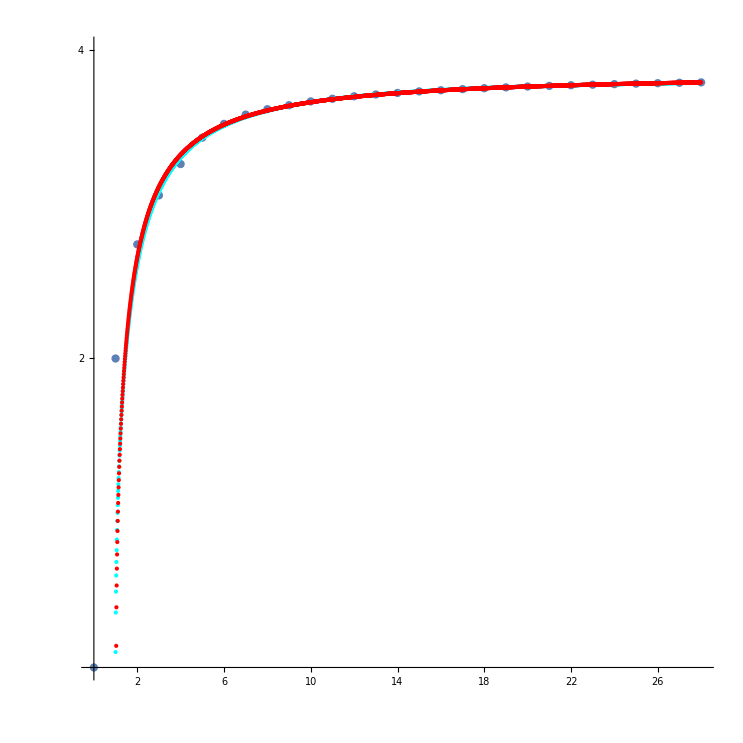

```mathematica
Show[ListPlot[Table[{i,Mnorm[i]},{i,0,Ntuple}],Ticks->{Range[2,Ntuple,2]},PlotStyle->{PointSize[.008]},AxesStyle->{Directive[Black,12,Thickness[.002]],Directive[Black,12,Thickness[.002]]},PlotRange->{0,4},AspectRatio->1],

ListPlot[Table[{x,Sqrt[14.7-26.787920033932256/(0.6+x)^1.2782407942281724]},{x,0.01,28,.01}],PlotStyle->{PointSize[.004],Dotted,Cyan}],
ListPlot[Table[{x,Sqrt[14.8-18.59750634048149/(0.19999999999999996+x)^1.1097159963858878]},{x,0.01,28,.01}],PlotStyle->{PointSize[.004],Dotted,Red}]]
```